# Off rates, run lengths and velocities as a function of load

This document compares the run lengths, velocities, and off rates of kinesin as a function of load, as measured by or stated in several papers, as well as those we use.

## This work

The parameter values I’m used to are

```mathematica
paramvals={v->1,dstep->8,fs->5,w->2,fd->4,a->1.07,b->.186,ϵ0->.7,ϵ0a->.7,fda->4,fsa->5};
```

### Stepping rate

from my definition

```mathematica
kstep[f_]:=Piecewise[{{v/dstep (1-(f/fs)^w),0<f<fs},{0,f≥fs},{v/dstep,f<0}}]
```

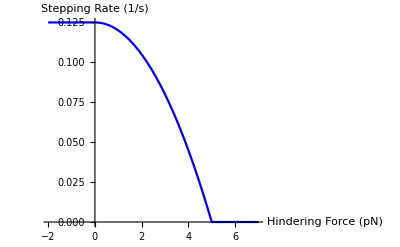

```mathematica
Plot[kstep[f]/.paramvals,{f,-2,7},AxesLabel->{"Hindering Force (pN)","Stepping Rate (1/s)"},PlotStyle->Blue]
```

translate to velocity

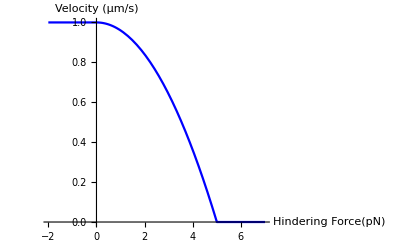

```mathematica
myvel=Plot[dstep*kstep[f]/.paramvals,{f,-2,7},AxesLabel->{"Hindering Force(pN)","Velocity (μm/s)"},PlotStyle->Blue]
myvelnm=Plot[1000*dstep*kstep[f]/.paramvals,{f,-2,7},AxesLabel->{"Hindering Force(pN)","Velocity (μm/s)"},PlotStyle->Blue];
```

### Run Length

My off rate

```mathematica
koff[f_]:=Piecewise[{{ϵ0 Exp[Abs[f]/fd],f≤fs},{a+b f,f>fs}}]
```

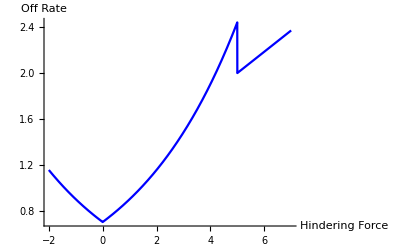

```mathematica
mykoff=Plot[koff[f]/.paramvals,{f,-2,7},AxesLabel->{"Hindering Force","Off Rate"},PlotStyle->Blue,PlotRange->{0,All}]
```

Then my run length is

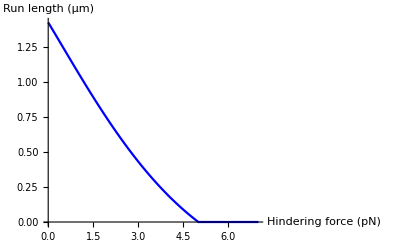

```mathematica
myrl=Plot[(dstep kstep[f])/koff[f]/.paramvals,{f,0,7},AxesLabel->{"Hindering force (pN)","Run length (μm)"},PlotStyle->Blue]
myrlnm=Plot[1000*(dstep kstep[f])/koff[f]/.paramvals,{f,0,7},AxesLabel->{"Hindering force (pN)","Run length (nm)"},PlotStyle->Blue];
```

## From Kunwar 2008 / Schnitzer 2000

Ambarish takes his run lengths and velocities from Schnizter 2000.  He writes down velocity from Michaelis-Menten (supplemental equation 2):

```mathematica
v[f_]:=kcat d ϵ[f]c/(c+km[f])
```

where

```mathematica
ϵ[f_]:=1-(f/f0)^2
```

```mathematica
km[f_]:=(kcat+koff0 Exp[f dl/(kB T)])/kon
```

From this we get step probabilities, and the detachment probabilities that depend on them (supplemental equation 3-5)

```mathematica
pstep[f_]:=kcat ϵ[f] c/(c+km[f])Δt
```

```mathematica
pdetach1[f_]:=b pstep[f]/c
```

```mathematica
pdetach2[f_]:=Exp[f δl/(kB T)]pstep[f]/a
```

The run length is given as (supplemental equation 6)

```mathematica
L[f_]:=d c a Exp[-f δl/(kB T)]/(c+b(1+a Exp[-f δl/(kB T)]))
```

with the parameters

```mathematica
k2008params={d->Quantity[8,"Nanometers"],δl->Quantity[1.3,"Nanometers"],b->Quantity[.029,"Micromolar"],a->107,kB->Quantity["BoltzmannConstant"],c->Quantity[3,"Millimolar"],T->Quantity[300,"Kelvins"],
koff0->Quantity[55,1/"Seconds"],dl->Quantity[1.6,"Nanometers"],kon->Quantity[2*^6,1/("Molar"*"Seconds")],kcat->Quantity[105,1/"Seconds"],f0->Quantity[8,"Piconewtons"],Δt->Quantity[1*^-5,"Seconds"]};
```

Then we can see how the two probabilities of detachment  change with force

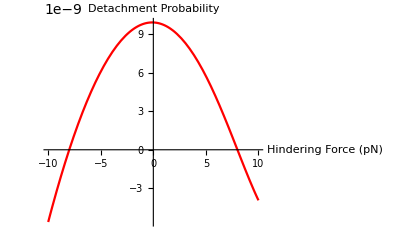

```mathematica
Plot[pdetach1[Quantity[f,"Piconewtons"]]/.k2008params,{f,-10,10},AxesLabel->{"Hindering Force (pN)","Detachment Probability"},PlotStyle->Red]
```

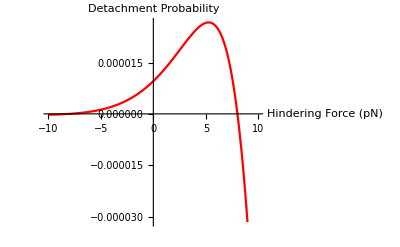

```mathematica
Plot[pdetach2[Quantity[f,"Piconewtons"]]/.k2008params,{f,-10,10},AxesLabel->{"Hindering Force (pN)","Detachment Probability"},PlotStyle->Red]
```

And the velocity

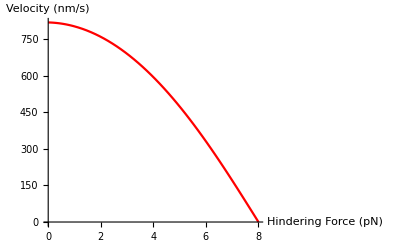

```mathematica
Svel=Plot[v[Quantity[f,"Piconewtons"]]/.k2008params,{f,0,8},PlotStyle->Red,AxesLabel->{"Hindering Force (pN)","Velocity (nm/s)"}]
```

This is quite different than mine:
my stall force is much lower
my unloaded velocity is higher

however, both are superlinear

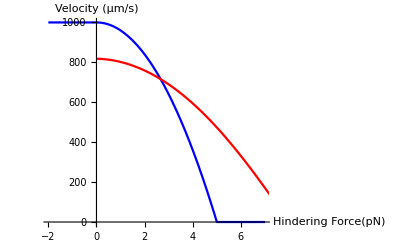

```mathematica
Show[{myvelnm,Svel}]
```

Run length as a function of force is

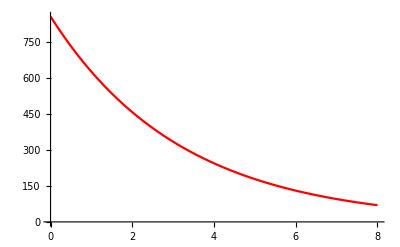

```mathematica
schnitzerrl=Plot[L[Quantity[f,"Piconewtons"]]/.k2008params,{f,0,8},PlotStyle->Red]
```

This is quite different than the run lengths in my model, for several reasons:
I put a hard stall at 5pN
My 0-force run lengths are much longer to match Michael and Jing’s results

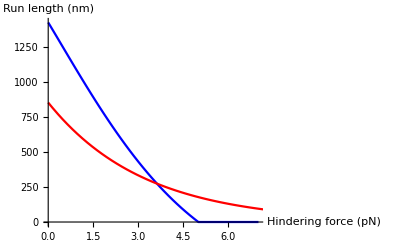

```mathematica
Show[{myrlnm,schnitzerrl}]
```

Then the effective koff is

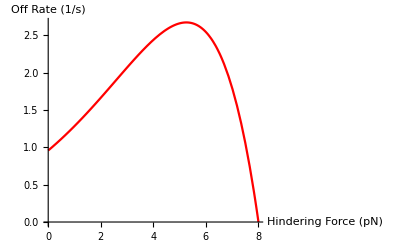

```mathematica
skoff=Plot[v[Quantity[f,"Piconewtons"]]/L[Quantity[f,"Piconewtons"]]/.k2008params,{f,0,8},AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"},PlotStyle->Red]
```

which is drastically different than mine. We’re using the off rate from Kunwar 2011 based on Gross lab measurements.

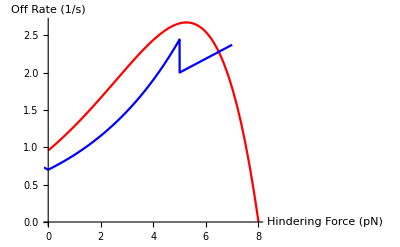

```mathematica
Show[{skoff,mykoff}]
```

## From Kunwar 2011

```mathematica
Kparamvals={v->1,dstep->8,fs->5,w->2,fd->4,a->1.07,b->.186,ϵ0->1};
```

Then his off rate is (fig S5)

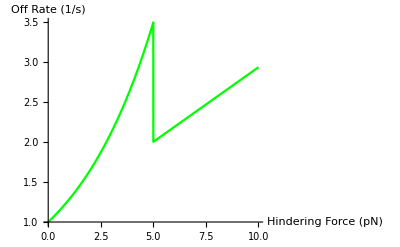

```mathematica
Plot[koff[f]/.Kparamvals,{f,0,10},AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"},PlotStyle->Green]
```

but his velocity is the same as mine, so his run lengths are

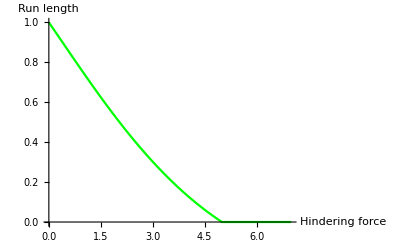

```mathematica
Krl=Plot[(dstep kstep[f])/koff[f]/.Kparamvals,{f,0,7},AxesLabel->{"Hindering force","Run length"},PlotStyle->Green]
```

Comparing to mine

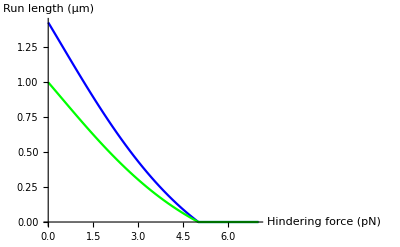

```mathematica
Show[{myrl,Krl}]
```

Unfortunately, neither Jing nor Michael have run lengths as a function of force that I can compare these to.

## From Andreasson 2015

Andreasson gives run lengths (figure 3), velocities (figure 5), and a separate figure of off rates (figure 6), which includes off rates above stall

```mathematica
Aparamvals={ϵ0->1.11,fd->QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"]*Quantity[300,"Kelvins"]/Quantity[.6,"Nanometers"],"Piconewtons"]],fsa->Infinity,fs->Infinity,ϵ0a->7.4,fda->QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"]*Quantity[300,"Kelvins"]/Quantity[.32,"Nanometers"],"Piconewtons"]],
kBT->QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"]*Quantity[300,"Kelvins"],"Piconewtons"*"Nanometers"]],dstep->8.3,Fi->26,k1->4900,k2->95,k3->260,δ1->4.6,δ3->.35,
l0->1120,δl->2,l0a->87,δla->.27}
```

{ϵ0→1.11,fd→6.90325,fsa→∞,fs→∞,ϵ0a→7.4,fda→12.9436,kBT→4.14195,dstep→8.3,Fi→26,k1→4900,k2→95,k3→260,δ1→4.6,δ3→0.35,l0→1120,δl→2,l0a→87,δla→0.27}

### Hindering

From figure 6

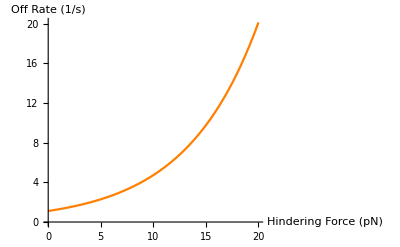

```mathematica
Aoff=Plot[koff[f]/.Aparamvals,{f,0,20},AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"},PlotStyle->Orange]
```

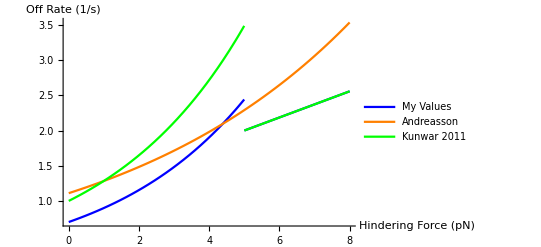

```mathematica
Plot[koff[f]/.{paramvals,Aparamvals,Kparamvals}//Evaluate,{f,0,8},PlotRange->{0,All},PlotStyle->{Blue,Orange,Green},AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"},PlotLegends->{"My Values","Andreasson","Kunwar 2011"}]
```

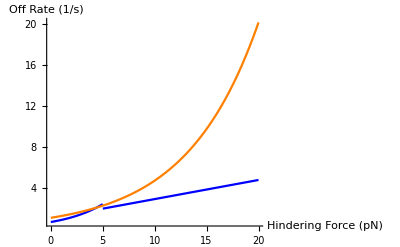

```mathematica
Plot[koff[f]/.{paramvals,Aparamvals}//Evaluate,{f,0,20},PlotRange->{0,All},PlotStyle->{Blue,Orange},AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"}]
```

### Assisting

From figure 6 / equation in the text

```mathematica
koffa[f_]:=Piecewise[{{ϵ0 Exp[Abs[f]/fd],0≤f≤fs},{a+b Abs[f],f>fs},{a+b Abs[f],f<-fsa},{ϵ0a Exp[Abs[f]/fda],0>f≥ -fsa}}]
```

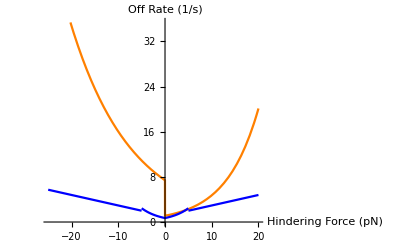

```mathematica
Plot[koffa[f]/.{Aparamvals,paramvals}//Evaluate,{f,-25,20},AxesLabel->{"Hindering Force (pN)","Off Rate (1/s)"},PlotStyle->{Orange,Blue}]
```

### Velocity

From the modeling section of the paper

```mathematica
vA[f_]:=dstep k1 k2 k3 Exp[(-f δ1+(-f+Fi)δ3)/(kBT)]/(k1 k2 Exp[-f δ1/(kBT)]+k3 Exp[(-f+Fi)δ3/(kBT)](k1 Exp[-f δ1/(kBT)]+k2))
```

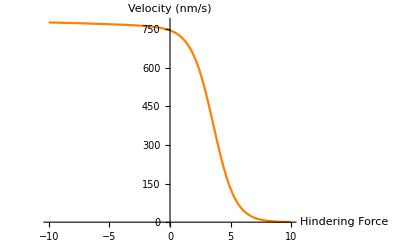

```mathematica
Plot[vA[f]/.Aparamvals,{f,10,-10},PlotRange->All,PlotStyle->Orange,AxesLabel->{"Hindering Force","Velocity (nm/s)"}]
```

### Run Length

Figure 3 / table 1

```mathematica
rlA[f_]:=Piecewise[{{l0a Exp[-Abs[f] δla/(kBT)],f<0},{l0 Exp[-Abs[f] δl/(kBT)],f>0}}]
```

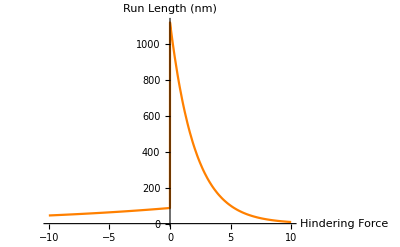

```mathematica
Plot[rlA[f]/.Aparamvals,{f,-10,10},PlotRange->All,PlotStyle->Orange,AxesLabel->{"Hindering Force","Run Length (nm)"}]
```

### Derived off rate

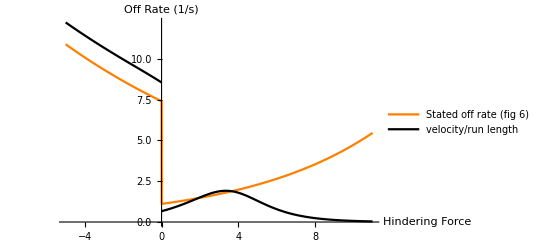

```mathematica
Plot[{koffa[f],vA[f]/rlA[f]}/.Aparamvals//Evaluate,{f,-5,11},PlotStyle->{Orange,Black},PlotLegends->{"Stated off rate (fig 6)","velocity/run length"},AxesLabel->{"Hindering Force","Off Rate (1/s)"}]
```

## Block 2003

Doesn’t seem to be any equations in the paper, so let’s just guess easy fits

```mathematica
Bparamvals={v0->668,v8r->580,v8l->430,rl0->1000,rl∞r->300,rl∞l->200,λr->.6,λl->.75}
```

{v0→668,v8r→580,v8l→430,rl0→1000,rl∞r→300,rl∞l→200,λr→0.6,λl→0.75}

Velocity looks pretty close to linear in the range of values shown

```mathematica
vB[f_]:=Piecewise[{{v0-(v0-v8r)/8f,f>0},{v0-(v0-v8l)/8Abs[f],f≤0}}]
```

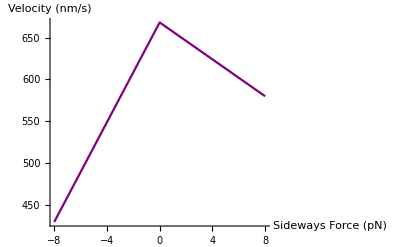

```mathematica
Plot[vB[f]/.Bparamvals,{f,-8,8},PlotRange->{0,All},PlotStyle->Purple,AxesLabel->{"Sideways Force (pN)","Velocity (nm/s)"}]
```

Run lengths look exponential

```mathematica
rlB[f_]:=Piecewise[{{(rl0-rl∞r) Exp[-λr Abs[f]]+rl∞r,f≥0},{(rl0-rl∞l) Exp[-λl Abs[f]]+rl∞l,f<0}}]
```

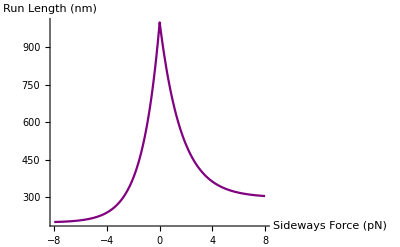

```mathematica
Plot[rlB[f]/.Bparamvals,{f,-8,8},PlotRange->{0,All},PlotStyle->Purple,AxesLabel->{"Sideways Force (pN)","Run Length (nm)"}]
```

Then we can derive an off rate

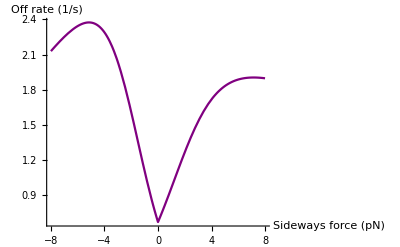

```mathematica
offrateB=Plot[vB[f]/rlB[f]/.Bparamvals,{f,-8,8},PlotRange->{0,All},PlotStyle->Purple,AxesLabel->{"Sideways force (pN)","Off rate (1/s)"}]
```

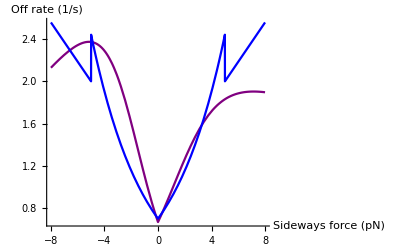

```mathematica
Plot[{vB[f]/rlB[f]/.Bparamvals,koff[Abs[f]]/.paramvals},{f,-8,8},PlotRange->{0,All},PlotStyle->{Purple,Blue},AxesLabel->{"Sideways force (pN)","Off rate (1/s)"}]
```

## Construct off rate as function of angle with MT

```mathematica
maxAngle[r_,l_]:=ArcSin[r/(r+l)]
```

```mathematica
maxAngle[.25,.08]/Degree
```

49.2509

At maxAngle backward it should look like Kunwar 2011
At maxAngle forward it should look like Andreasson 2015
At maxAngle left and right it should look like Block 2003
Michael pulled straight up in his Tau paper, but it was only an instantaneous pull and on a multiple motor cargo

Parameter values

```mathematica
ultparamvals={fd->QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"]*Quantity[300,"Kelvins"]/Quantity[.6,"Nanometers"],"Piconewtons"]],fs->Infinity,ϵ0a->7.4,a->1.07,b->.186,ϵ0->.7,fsa->Infinity,ϵ0a->7.4,fda->QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"]*Quantity[300,"Kelvins"]/Quantity[.32,"Nanometers"],"Piconewtons"]],
v0->668,v8r->580,v8l->430,rl0->1000,rl∞r->300,rl∞l->200,λr->.6,λl->.75}
```

{fd→6.90325,fs→∞,ϵ0a→7.4,a→1.07,b→0.186,ϵ0→0.7,fsa→∞,ϵ0a→7.4,fda→12.9436,v0→668,v8r→580,v8l→430,rl0→1000,rl∞r→300,rl∞l→200,λr→0.6,λl→0.75}

Off rate as a function of azimuthal angle

```mathematica
ultOff[f_,θ_]:=Piecewise[{{((θ-0)/(Pi/2))*koffa[-f]+((Pi/2-θ)/(Pi/2))*vB[f]/rlB[f],0<=θ<=Pi/2},
{((θ-Pi/2)/(Pi/2))*vB[-f]/rlB[-f]+((Pi-θ)/(Pi/2))*koffa[-f],Pi/2<θ<=Pi},
{((θ-Pi)/(Pi/2))*koff[f]+((3Pi/2-θ)/(Pi/2))*vB[-f]/rlB[-f],Pi<θ<=3Pi/2},
{((θ-3Pi/2)/(Pi/2))*vB[f]/rlB[f]+((2Pi-θ)/(Pi/2))*koff[f],3Pi/2<θ<=2Pi}}]
```

Off rate with azimuthal and elevation angle

```mathematica
ultOff2[f_,θ_,ϕ_]:=Piecewise[{{((ϕ-maxAngle[.25,.08])/(Pi/2-maxAngle[.25,.08]))*koff[f]+
((Pi/2-ϕ)/(Pi/2-maxAngle[.25,.08]))*ultOff[f,θ],maxAngle[.25,.08]≤ϕ≤ Pi/2},
{ultOff[f,θ],0≤ϕ< maxAngle[.25,.08]}}]
```

```mathematica
ultOff2[0,0,ϕ]
```

Piecewise[{{(1.40606 v0 (π/2-ϕ))/rl0+1.40606 (-0.859591+ϕ) (Piecewise[{{ϵ0, 0≤fs}, {a, 0>fs}, {0, True}}]), 0.859591≤ϕ≤π/2}, {v0/rl0, 0≤ϕ<0.859591}, {0, True}}]

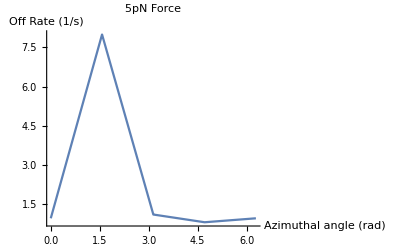

```mathematica
Plot[ultOff2[1,θ,0]/.ultparamvals,{θ,0,2Pi},AxesLabel->{"Azimuthal angle (rad)","Off Rate (1/s)"},PlotLabel-> "5pN Force",PlotRange->{0,All}]
```

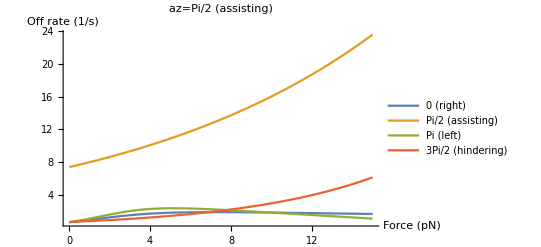

```mathematica
Plot[Evaluate[ultOff[f,#]&/@{0,Pi/2,Pi,3Pi/2}/.ultparamvals],{f,0,15},AxesLabel->{"Force (pN)","Off rate (1/s)"},PlotLabel->"az=Pi/2 (assisting)",PlotRange->{0,All},PlotLegends->{"0 (right)","Pi/2 (assisting)","Pi (left)","3Pi/2 (hindering)"}]
```

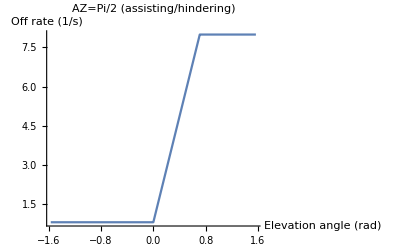

```mathematica
Plot[ultOff2[1,Piecewise[{{Pi/2,α≥0},{3Pi/2,α<0}}],Pi/2-Abs[α]]/.ultparamvals,{α,-Pi/2,Pi/2},PlotRange->{0,All},AxesLabel->{"Elevation angle (rad)","Off rate (1/s)"},PlotLabel->"AZ=Pi/2 (assisting/hindering)"]
```

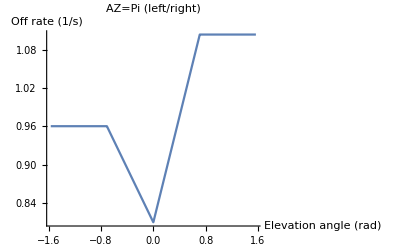

```mathematica
Plot[ultOff2[1,Piecewise[{{Pi,α≥0},{2Pi,α<0}}],Pi/2-Abs[α]]/.ultparamvals,{α,-Pi/2,Pi/2},PlotRange->{0,All},AxesLabel->{"Elevation angle (rad)","Off rate (1/s)"},PlotLabel->"AZ=Pi (left/right)"]
```

```mathematica
ParametricPlot3D[{r Cos[t],r Sin[t],ultOff[r,t]/.ultparamvals},{r,0,15},{t,0,2Pi},AxesLabel->{"Rightward Load (pN)","Assisting Load (pN)","Off Rate (1/s)"}]
```

-Graphics3D-

```mathematica
Manipulate[ParametricPlot3D[{r Cos[t],r Sin[t],ultOff2[r,t,ϕ]/.ultparamvals},{r,0,15},{t,0,2Pi},AxesLabel->{"Rightward Load (pN)","Assisting Load (pN)","Off Rate (1/s)"}],{ϕ,0,Pi/2}]
```

ReplaceAll::reps: {ultparamvals} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {ultparamvals} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.